# Parallel Raw Pattern Search: (a,c) = (5,1)

This notebook performs the approved fast, safeguarded refinement test at (a,c) = (5,1). The exciton uses its analytical kinetic term and independently integrated Coulomb numerator and norm. The biexciton uses the completely raw P+Q, six-term Coulomb, and four-particle kinetic expressions. Only the redundant global rotation is removed by setting phi_a = 0; all three remaining relative angles cover the full [0,2 Pi] range, with no reflection folding or particle-exchange multiplicities.

Independent parameter candidates run on eight parallel subkernels. Within each candidate, the numerator and denominator remain separate AdaptiveQuasiMonteCarlo integrations with no fixed shared Sobol points. The master kernel checkpoints every candidate as soon as it finishes. A stopped stage can therefore be evaluated again; completed candidates are reused and only missing candidates are submitted.

The X scan uses 2,000,000 MaxPoints at five initial alpha values and then at two half-step points around the best initial value. The XX scan uses 1,000,000 MaxPoints at the current center and its eight coordinate neighbors. The best proposed move is checked at 2,000,000 MaxPoints and is accepted only if it is lower at both budgets and its high-budget improvement exceeds both 0.02 Ry and the observed cross-budget disagreement. A half-step refinement then tests the two most promising coordinate directions and applies the same final verification rule.

Run the cells in order. The existing 1,000,000- and 2,000,000-point raw XX evaluations at the starting center are imported automatically when available.

## Load and review

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Main-State-Raw-Pattern-Search-a5-c1.wl"}]]
```

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Parallel raw pattern search loaded for (a,c) = (5,1). Existing XX center evaluations reused: 2. Review psConfiguration[], then run psPrepareKernels[].

```mathematica
psConfiguration[]
```

<|implementation→parallel-raw-pattern-search-v1,geometry→<|a→5.,c→1.|>,workers→8,XBudget→2000000,XXSearchBudget→1000000,XXVerifyBudget→2000000,minimumImprovementRy→0.02,refinementDirectionCount→2,startXAlpha→0.731089,startXXParameters→{0.679864,0.153779,2.49296,2.10885},XStep→0.0511763,XXSteps→{0.0815837,0.0384449,0.199437,0.210885},XInitialParameters→{{0.628737},{0.679913},{0.731089},{0.782266},{0.833442}},XXInitialParameters→{{0.679864,0.153779,2.49296,2.10885},{0.598281,0.153779,2.49296,2.10885},{0.761448,0.153779,2.49296,2.10885},{0.679864,0.115335,2.49296,2.10885},{0.679864,0.192224,2.49296,2.10885},{0.679864,0.153779,2.29353,2.10885},{0.679864,0.153779,2.6924,2.10885},{0.679864,0.153779,2.49296,1.89796},{0.679864,0.153779,2.49296,2.31973}},angularTreatment→phi_a=0; all remaining relative angles cover [0,2 Pi],sampling→independent adaptive QMC calls for numerator and denominator|>

```mathematica
psPrepareKernels[]
```

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

Staged global-rotation-fixed raw minimization loaded at (a,c) = {5.,1.}. Optimization MaxPoints = 100000; final MaxPoints = 2000000. Warm start: <|XAlpha→{0.652964},XXParameters→{0.679864,0.153779,2.49296,2.30885}|>. Run rawMinimizeX[], rawMinimizeXX[], then rawMinFinalize[].

«5 more identical outputs»

Parallel workers prepared: 8. Source loaded successfully on all workers: True

<|processorCount→10,kernelCount→8,loaded→True|>

## Exciton: high-budget scan

The first cell evaluates the five-point scan. The second displays it. The third evaluates two half-step points around the best initial alpha, and the fourth displays the combined result.

```mathematica
psRunXInitial[]
```

X-initial-grid: 5 requested; 5 missing; 0 reused.

X-initial-grid: completed 0.8334419257672615 on kernel 15; correction = -2.33634; remaining = 4

X-initial-grid: completed 0.628736891368285 on kernel 11; correction = -2.34321; remaining = 3

X-initial-grid: completed 0.6799131499680291 on kernel 12; correction = -2.35194; remaining = 2

X-initial-grid: completed 0.7822656671675174 on kernel 14; correction = -2.35192; remaining = 1

X-initial-grid: completed 0.7310894085677733 on kernel 13; correction = -2.35507; remaining = 0

{<|candidateKey→X::2000000::0.628736891368285,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.628737},parameterKey→0.628736891368285,norm→0.200731,numeratorRy→-0.56152,analyticKineticRy→0.454167,correctionRy→-2.34321,elapsedSeconds→404.274,workerKernel→11,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:25,integrals→{<|integral→normDenominator,seconds→152.135,value→0.200731,hitMaxPoints→True,relativeErrorEstimate→0.000717977,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.200731 and 0.00014412
     for the integral and error estimates.,messageIntegralEstimate→0.200731,reportedErrorEstimate→0.00014412|>,<|integral→coulombNumerator,seconds→252.139,value→-0.56152,hitMaxPoints→True,relativeErrorEstimate→0.00159176,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.56152 and 0.000893807
     for the integral and error estimates.,messageIntegralEstimate→-0.56152,reportedErrorEstimate→0.000893807|>}|>,<|candidateKey→X::2000000::0.6799131499680291,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.679913},parameterKey→0.6799131499680291,norm→0.181194,numeratorRy→-0.522392,analyticKineticRy→0.531111,correctionRy→-2.35194,elapsedSeconds→404.228,workerKernel→12,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:25,integrals→{<|integral→normDenominator,seconds→151.61,value→0.181194,hitMaxPoints→True,relativeErrorEstimate→0.000776802,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.181194 and 0.000140752
     for the integral and error estimates.,messageIntegralEstimate→0.181194,reportedErrorEstimate→0.000140752|>,<|integral→coulombNumerator,seconds→252.618,value→-0.522392,hitMaxPoints→True,relativeErrorEstimate→0.00166751,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.522392 and 0.000871094
     for the integral and error estimates.,messageIntegralEstimate→-0.522392,reportedErrorEstimate→0.000871094|>}|>,<|candidateKey→X::2000000::0.7310894085677733,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.731089},parameterKey→0.7310894085677733,norm→0.164087,numeratorRy→-0.487197,analyticKineticRy→0.614072,correctionRy→-2.35507,elapsedSeconds→405.329,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:26,integrals→{<|integral→normDenominator,seconds→152.237,value→0.164087,hitMaxPoints→True,relativeErrorEstimate→0.000828067,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.164087 and 0.000135875
     for the integral and error estimates.,messageIntegralEstimate→0.164087,reportedErrorEstimate→0.000135875|>,<|integral→coulombNumerator,seconds→253.092,value→-0.487197,hitMaxPoints→True,relativeErrorEstimate→0.00171845,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.487197 and 0.000837225
     for the integral and error estimates.,messageIntegralEstimate→-0.487197,reportedErrorEstimate→0.000837225|>}|>,<|candidateKey→X::2000000::0.7822656671675174,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.782266},parameterKey→0.7822656671675174,norm→0.149035,numeratorRy→-0.455297,analyticKineticRy→0.703051,correctionRy→-2.35192,elapsedSeconds→404.272,workerKernel→14,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:25,integrals→{<|integral→normDenominator,seconds→152.77,value→0.149035,hitMaxPoints→True,relativeErrorEstimate→0.000881727,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.149035 and 0.000131408
     for the integral and error estimates.,messageIntegralEstimate→0.149035,reportedErrorEstimate→0.000131408|>,<|integral→coulombNumerator,seconds→251.502,value→-0.455297,hitMaxPoints→True,relativeErrorEstimate→0.00179128,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.455297 and 0.000815566
     for the integral and error estimates.,messageIntegralEstimate→-0.455297,reportedErrorEstimate→0.000815566|>}|>,<|candidateKey→X::2000000::0.8334419257672615,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.833442},parameterKey→0.8334419257672615,norm→0.135776,numeratorRy→-0.425575,analyticKineticRy→0.798047,correctionRy→-2.33634,elapsedSeconds→404.018,workerKernel→15,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:24,integrals→{<|integral→normDenominator,seconds→151.988,value→0.135776,hitMaxPoints→True,relativeErrorEstimate→0.000931782,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.135776 and 0.000126514
     for the integral and error estimates.,messageIntegralEstimate→0.135776,reportedErrorEstimate→0.000126514|>,<|integral→coulombNumerator,seconds→252.03,value→-0.425575,hitMaxPoints→True,relativeErrorEstimate→0.00185921,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.425575 and 0.000791235
     for the integral and error estimates.,messageIntegralEstimate→-0.425575,reportedErrorEstimate→0.000791235|>}|>}

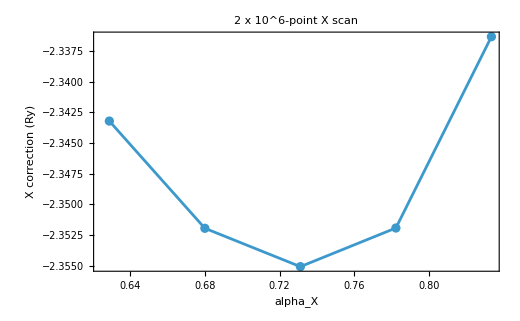

```mathematica
psXPlot[]
```

```mathematica
psRunXRefinement[]
```

X-half-step-refinement: 2 requested; 2 missing; 0 reused.

X-half-step-refinement: completed 0.7566775378676454 on kernel 12; correction = -2.35164; remaining = 1

X-half-step-refinement: completed 0.7055012792679012 on kernel 11; correction = -2.35164; remaining = 0

{<|candidateKey→X::2000000::0.7055012792679012,stage→X-half-step-refinement,system→X,budget→2000000,parameters→{0.705501},parameterKey→0.7055012792679012,norm→0.172382,numeratorRy→-0.503956,analyticKineticRy→0.571839,correctionRy→-2.35164,elapsedSeconds→258.786,workerKernel→11,status→complete,source→parallel-pattern-search,started→2026-07-31T21:00:26,completed→2026-07-31T21:04:45,integrals→{<|integral→normDenominator,seconds→109.209,value→0.172382,hitMaxPoints→True,relativeErrorEstimate→0.000805622,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.172382 and 0.000138875
     for the integral and error estimates.,messageIntegralEstimate→0.172382,reportedErrorEstimate→0.000138875|>,<|integral→coulombNumerator,seconds→149.578,value→-0.503956,hitMaxPoints→True,relativeErrorEstimate→0.00169097,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.503956 and 0.000852172
     for the integral and error estimates.,messageIntegralEstimate→-0.503956,reportedErrorEstimate→0.000852172|>}|>,<|candidateKey→X::2000000::0.7566775378676454,stage→X-half-step-refinement,system→X,budget→2000000,parameters→{0.756678},parameterKey→0.7566775378676454,norm→0.15633,numeratorRy→-0.470466,analyticKineticRy→0.657809,correctionRy→-2.35164,elapsedSeconds→257.208,workerKernel→12,status→complete,source→parallel-pattern-search,started→2026-07-31T21:00:26,completed→2026-07-31T21:04:43,integrals→{<|integral→normDenominator,seconds→108.596,value→0.15633,hitMaxPoints→True,relativeErrorEstimate→0.000852467,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.15633 and 0.000133266
     for the integral and error estimates.,messageIntegralEstimate→0.15633,reportedErrorEstimate→0.000133266|>,<|integral→coulombNumerator,seconds→148.612,value→-0.470466,hitMaxPoints→True,relativeErrorEstimate→0.00176766,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.470466 and 0.000831623
     for the integral and error estimates.,messageIntegralEstimate→-0.470466,reportedErrorEstimate→0.000831623|>}|>}

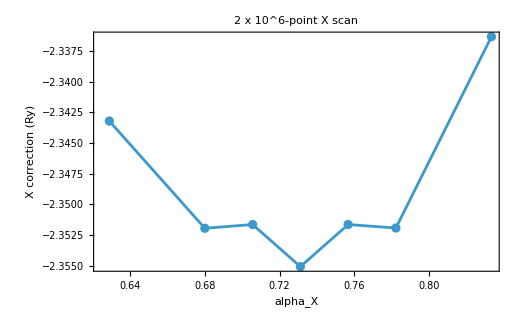

```mathematica
psXPlot[]
```

```mathematica
psBestXRow[]
```

<|candidateKey→X::2000000::0.7310894085677733,stage→X-initial-grid,system→X,budget→2000000,parameters→{0.731089},parameterKey→0.7310894085677733,norm→0.164087,numeratorRy→-0.487197,analyticKineticRy→0.614072,correctionRy→-2.35507,elapsedSeconds→405.329,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-07-31T20:53:40,completed→2026-07-31T21:00:26,integrals→{<|integral→normDenominator,seconds→152.237,value→0.164087,hitMaxPoints→True,relativeErrorEstimate→0.000828067,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained 0.164087 and 0.000135875
     for the integral and error estimates.,messageIntegralEstimate→0.164087,reportedErrorEstimate→0.000135875|>,<|integral→coulombNumerator,seconds→253.092,value→-0.487197,hitMaxPoints→True,relativeErrorEstimate→0.00171845,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 2000100
     integrand evaluations. NIntegrate obtained -0.487197 and 0.000837225
     for the integral and error estimates.,messageIntegralEstimate→-0.487197,reportedErrorEstimate→0.000837225|>}|>

## Biexciton: initial coordinate stencil

This stage evaluates the eight missing coordinate neighbors at 1,000,000 MaxPoints. The already computed center is reused. Each small plot shows the minus, center, and plus result along one parameter direction.

```mathematica
psRunXXInitial[]
```

XX-initial-stencil: 9 requested; 8 missing; 1 reused.

XX-initial-stencil: completed 0.6798642956307124|0.15377949033301186|2.6924003294158902|2.1088466287924317 on kernel 16; correction = -4.85796; remaining = 7

XX-initial-stencil: completed 0.6798642956307124|0.15377949033301186|2.492963267977676|2.319731291671675 on kernel 18; correction = -4.82692; remaining = 6

XX-initial-stencil: completed 0.6798642956307124|0.15377949033301186|2.492963267977676|1.8979619659131886 on kernel 17; correction = -4.85874; remaining = 5

XX-initial-stencil: completed 0.6798642956307124|0.15377949033301186|2.293526206539462|2.1088466287924317 on kernel 15; correction = -4.8306; remaining = 4

XX-initial-stencil: completed 0.6798642956307124|0.19222436291626482|2.492963267977676|2.1088466287924317 on kernel 14; correction = -4.83483; remaining = 3

XX-initial-stencil: completed 0.5982805801550269|0.15377949033301186|2.492963267977676|2.1088466287924317 on kernel 11; correction = -4.88563; remaining = 2

XX-initial-stencil: completed 0.7614480111063978|0.15377949033301186|2.492963267977676|2.1088466287924317 on kernel 12; correction = -4.8475; remaining = 1

XX-initial-stencil: completed 0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317 on kernel 13; correction = -4.90873; remaining = 0

{<|candidateKey→XX::1000000::0.6798642956307124|0.15377949033301186|2.492963267977676|2.1088466287924317,stage→seed-existing-center,system→XX,budget→1000000,parameters→{0.679864,0.153779,2.49296,2.10885},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|2.1088466287924317,norm→0.000552495,numeratorRy→-0.00268689,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.8632,elapsedSeconds→3413.76,workerKernel→Missing[Historical],status→complete,source→main-state-raw-gauge-trial-a5-c1,started→Missing[Historical],completed→Missing[Historical],integrals→{<|integral→normDenominator,seconds→216.79,value→0.000552495,hitMaxPoints→True,messageIntegralEstimate→Missing[NotAvailable],reportedErrorEstimate→Missing[NotAvailable],relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000552495 and 1.19398 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→3196.97,value→-0.00268689,hitMaxPoints→True,messageIntegralEstimate→Missing[NotAvailable],reportedErrorEstimate→Missing[NotAvailable],relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00268689 and 9.69593 10
     for the integral and error estimates.|>}|>,<|candidateKey→XX::1000000::0.5982805801550269|0.15377949033301186|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.598281,0.153779,2.49296,2.10885},parameterKey→0.5982805801550269|0.15377949033301186|2.492963267977676|2.1088466287924317,norm→0.000772315,numeratorRy→-0.00377324,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.88563,elapsedSeconds→10217.7,workerKernel→11,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:55:03,integrals→{<|integral→normDenominator,seconds→622.216,value→0.000772315,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000772315 and 1.55319 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9595.47,value→-0.00377324,hitMaxPoints→True,relativeErrorEstimate→0.00335785,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00377324 and 0.00001267
     for the integral and error estimates.,messageIntegralEstimate→-0.00377324,reportedErrorEstimate→0.00001267|>}|>,<|candidateKey→XX::1000000::0.7614480111063978|0.15377949033301186|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.761448,0.153779,2.49296,2.10885},parameterKey→0.7614480111063978|0.15377949033301186|2.492963267977676|2.1088466287924317,norm→0.000400442,numeratorRy→-0.00194114,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.8475,elapsedSeconds→10229.2,workerKernel→12,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:55:14,integrals→{<|integral→normDenominator,seconds→624.165,value→0.000400442,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000400442 and 9.34339 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9604.99,value→-0.00194114,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00194114 and 7.42596 10
     for the integral and error estimates.|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.115335,2.49296,2.10885},parameterKey→0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,norm→0.000658438,numeratorRy→-0.0032321,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.90873,elapsedSeconds→10230.3,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:55:15,integrals→{<|integral→normDenominator,seconds→623.74,value→0.000658438,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000658438 and 1.37662 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9606.55,value→-0.0032321,hitMaxPoints→True,relativeErrorEstimate→0.00348808,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0032321 and 0.0000112738
     for the integral and error estimates.,messageIntegralEstimate→-0.0032321,reportedErrorEstimate→0.0000112738|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.19222436291626482|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.192224,2.49296,2.10885},parameterKey→0.6798642956307124|0.19222436291626482|2.492963267977676|2.1088466287924317,norm→0.0004649,numeratorRy→-0.00224771,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.83483,elapsedSeconds→10198.2,workerKernel→14,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:54:43,integrals→{<|integral→normDenominator,seconds→619.671,value→0.0004649,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                        -6
     integrand evaluations. NIntegrate obtained 0.0004649 and 1.04527 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9578.48,value→-0.00224771,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00224771 and 8.28906 10
     for the integral and error estimates.|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.15377949033301186|2.293526206539462|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.153779,2.29353,2.10885},parameterKey→0.6798642956307124|0.15377949033301186|2.293526206539462|2.1088466287924317,norm→0.000529838,numeratorRy→-0.00255944,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.8306,elapsedSeconds→10195.7,workerKernel→15,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:54:41,integrals→{<|integral→normDenominator,seconds→621.825,value→0.000529838,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000529838 and 1.19069 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9573.88,value→-0.00255944,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00255944 and 9.69078 10
     for the integral and error estimates.|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.15377949033301186|2.6924003294158902|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.153779,2.6924,2.10885},parameterKey→0.6798642956307124|0.15377949033301186|2.6924003294158902|2.1088466287924317,norm→0.000588736,numeratorRy→-0.00286006,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.85796,elapsedSeconds→10145.4,workerKernel→16,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:53:50,integrals→{<|integral→normDenominator,seconds→612.649,value→0.000588736,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000588736 and 1.24064 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9532.74,value→-0.00286006,hitMaxPoints→True,relativeErrorEstimate→0.00351489,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00286006 and 0.0000100528
     for the integral and error estimates.,messageIntegralEstimate→-0.00286006,reportedErrorEstimate→0.0000100528|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.15377949033301186|2.492963267977676|1.8979619659131886,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.153779,2.49296,1.89796},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|1.8979619659131886,norm→0.000936912,numeratorRy→-0.00455221,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.85874,elapsedSeconds→10171.2,workerKernel→17,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:54:16,integrals→{<|integral→normDenominator,seconds→615.35,value→0.000936912,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000936912 and 1.92547 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9555.84,value→-0.00455221,hitMaxPoints→True,relativeErrorEstimate→0.00340215,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00455221 and 0.0000154873
     for the integral and error estimates.,messageIntegralEstimate→-0.00455221,reportedErrorEstimate→0.0000154873|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.15377949033301186|2.492963267977676|2.319731291671675,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.153779,2.49296,2.31973},parameterKey→0.6798642956307124|0.15377949033301186|2.492963267977676|2.319731291671675,norm→0.000336394,numeratorRy→-0.00162374,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.82692,elapsedSeconds→10152.1,workerKernel→18,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:53:57,integrals→{<|integral→normDenominator,seconds→615.141,value→0.000336394,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -7
     integrand evaluations. NIntegrate obtained 0.000336394 and 7.72161 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9536.98,value→-0.00162374,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00162374 and 6.20103 10
     for the integral and error estimates.|>}|>}

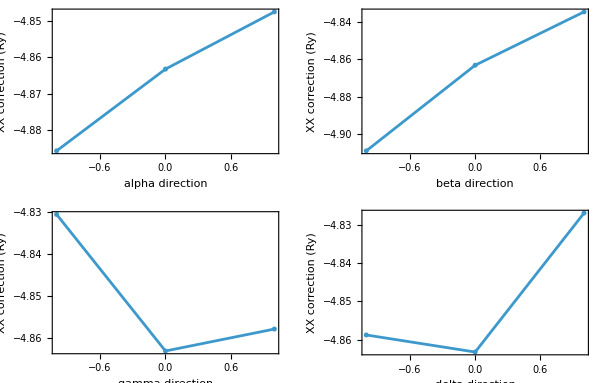

```mathematica
psXXInitialPlot[]
```

```mathematica
psXXAxisScores[]
```

{<|axis→1,scoreRy→-0.0224344|>,<|axis→2,scoreRy→-0.0455355|>,<|axis→3,scoreRy→0.00523398|>,<|axis→4,scoreRy→0.00445517|>}

## Biexciton: verify the first proposed move

The lowest 1,000,000-point candidate is re-evaluated at 2,000,000 MaxPoints. The returned association reports both energy differences, their disagreement, the acceptance threshold, and whether the center moves.

```mathematica
psRunXXVerification[]
```

XX-first-verification: 2 requested; 1 missing; 1 reused.

XX-first-verification: completed 0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317 on kernel 11; correction = -4.901; remaining = 0

<|status→complete,centerParameters→{0.679864,0.153779,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.8632,candidateLowRy→-4.90873,centerHighRy→-4.8631,candidateHighRy→-4.901,deltaLowRy→-0.0455355,deltaHighRy→-0.0378964,crossBudgetDisagreementRy→0.00763904,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>

```mathematica
psXXFirstDecision[]
```

<|status→complete,centerParameters→{0.679864,0.153779,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.8632,candidateLowRy→-4.90873,centerHighRy→-4.8631,candidateHighRy→-4.901,deltaLowRy→-0.0455355,deltaHighRy→-0.0378964,crossBudgetDisagreementRy→0.00763904,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>

```mathematica
psXXAcceptedCenter[]
```

{0.679864,0.115335,2.49296,2.10885}

## Biexciton: half-step directional refinement

The two directions with the strongest initial decrease are refined with half steps around the accepted center. The best low-budget refinement is then checked at 2,000,000 MaxPoints using the same safeguarded acceptance rule.

```mathematica
psXXRefinementAxes[]
```

{2,1}

```mathematica
psRunXXRefinement[]
```

XX-directional-refinement: 4 requested; 4 missing; 0 reused.

XX-directional-refinement: completed 0.7206561533685552|0.1153346177497589|2.492963267977676|2.1088466287924317 on kernel 14; correction = -4.88655; remaining = 3

XX-directional-refinement: completed 0.6798642956307124|0.13455705404138538|2.492963267977676|2.1088466287924317 on kernel 12; correction = -4.88331; remaining = 2

XX-directional-refinement: completed 0.6390724378928696|0.1153346177497589|2.492963267977676|2.1088466287924317 on kernel 13; correction = -4.89571; remaining = 1

XX-directional-refinement: completed 0.6798642956307124|0.09611218145813241|2.492963267977676|2.1088466287924317 on kernel 11; correction = -4.90357; remaining = 0

{<|candidateKey→XX::1000000::0.6798642956307124|0.09611218145813241|2.492963267977676|2.1088466287924317,stage→XX-directional-refinement,system→XX,budget→1000000,parameters→{0.679864,0.0961122,2.49296,2.10885},parameterKey→0.6798642956307124|0.09611218145813241|2.492963267977676|2.1088466287924317,norm→0.000720884,numeratorRy→-0.00353491,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.90357,elapsedSeconds→6899.61,workerKernel→11,status→complete,source→parallel-pattern-search,started→2026-08-01T01:51:30,completed→2026-08-01T03:46:29,integrals→{<|integral→normDenominator,seconds→415.111,value→0.000720884,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000720884 and 1.48716 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→6484.5,value→-0.00353491,hitMaxPoints→True,relativeErrorEstimate→0.00343868,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00353491 and 0.0000121554
     for the integral and error estimates.,messageIntegralEstimate→-0.00353491,reportedErrorEstimate→0.0000121554|>}|>,<|candidateKey→XX::1000000::0.6798642956307124|0.13455705404138538|2.492963267977676|2.1088466287924317,stage→XX-directional-refinement,system→XX,budget→1000000,parameters→{0.679864,0.134557,2.49296,2.10885},parameterKey→0.6798642956307124|0.13455705404138538|2.492963267977676|2.1088466287924317,norm→0.000603606,numeratorRy→-0.00294759,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.88331,elapsedSeconds→6886.33,workerKernel→12,status→complete,source→parallel-pattern-search,started→2026-08-01T01:51:30,completed→2026-08-01T03:46:16,integrals→{<|integral→normDenominator,seconds→408.536,value→0.000603606,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000603606 and 1.28659 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→6477.79,value→-0.00294759,hitMaxPoints→True,relativeErrorEstimate→0.00354727,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00294759 and 0.0000104559
     for the integral and error estimates.,messageIntegralEstimate→-0.00294759,reportedErrorEstimate→0.0000104559|>}|>,<|candidateKey→XX::1000000::0.6390724378928696|0.1153346177497589|2.492963267977676|2.1088466287924317,stage→XX-directional-refinement,system→XX,budget→1000000,parameters→{0.639072,0.115335,2.49296,2.10885},parameterKey→0.6390724378928696|0.1153346177497589|2.492963267977676|2.1088466287924317,norm→0.000780992,numeratorRy→-0.00382351,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.89571,elapsedSeconds→6898.83,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-08-01T01:51:30,completed→2026-08-01T03:46:29,integrals→{<|integral→normDenominator,seconds→410.477,value→0.000780992,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000780992 and 1.57641 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→6488.35,value→-0.00382351,hitMaxPoints→True,relativeErrorEstimate→0.00340585,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.00382351 and 0.0000130223
     for the integral and error estimates.,messageIntegralEstimate→-0.00382351,reportedErrorEstimate→0.0000130223|>}|>,<|candidateKey→XX::1000000::0.7206561533685552|0.1153346177497589|2.492963267977676|2.1088466287924317,stage→XX-directional-refinement,system→XX,budget→1000000,parameters→{0.720656,0.115335,2.49296,2.10885},parameterKey→0.7206561533685552|0.1153346177497589|2.492963267977676|2.1088466287924317,norm→0.000559614,numeratorRy→-0.00273458,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.88655,elapsedSeconds→6869.43,workerKernel→14,status→complete,source→parallel-pattern-search,started→2026-08-01T01:51:30,completed→2026-08-01T03:45:59,integrals→{<|integral→normDenominator,seconds→407.067,value→0.000559614,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000559614 and 1.21461 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→6462.36,value→-0.00273458,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained -0.00273458 and 9.90586 10
     for the integral and error estimates.|>}|>}

```mathematica
psRunXXFinalVerification[]
```

XX-final-verification: 1 requested; 0 missing; 1 reused.

<|status→complete,centerParameters→{0.679864,0.115335,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.90873,candidateLowRy→-4.90873,centerHighRy→-4.901,candidateHighRy→-4.901,deltaLowRy→0.,deltaHighRy→0.,crossBudgetDisagreementRy→0.,acceptanceThresholdRy→0.02,accepted→False,reason→center remained best|>

```mathematica
psXXFinalDecision[]
```

<|status→complete,centerParameters→{0.679864,0.115335,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.90873,candidateLowRy→-4.90873,centerHighRy→-4.901,candidateHighRy→-4.901,deltaLowRy→0.,deltaHighRy→0.,crossBudgetDisagreementRy→0.,acceptanceThresholdRy→0.02,accepted→False,reason→center remained best|>

## Results and timing

The summary gives the selected X alpha, both XX decisions, and the final XX parameters. The candidate table contains total elapsed time per parameter point. The integrals CSV contains separate timings, values, error estimates, and warnings for every numerator and denominator.

```mathematica
psSummary[]
```

<|configuration→<|implementation→parallel-raw-pattern-search-v1,geometry→<|a→5.,c→1.|>,workers→8,XBudget→2000000,XXSearchBudget→1000000,XXVerifyBudget→2000000,minimumImprovementRy→0.02,refinementDirectionCount→2,startXAlpha→0.731089,startXXParameters→{0.679864,0.153779,2.49296,2.10885},XStep→0.0511763,XXSteps→{0.0815837,0.0384449,0.199437,0.210885},XInitialParameters→{{0.628737},{0.679913},{0.731089},{0.782266},{0.833442}},XXInitialParameters→{{0.679864,0.153779,2.49296,2.10885},{0.598281,0.153779,2.49296,2.10885},{0.761448,0.153779,2.49296,2.10885},{0.679864,0.115335,2.49296,2.10885},{0.679864,0.192224,2.49296,2.10885},{0.679864,0.153779,2.29353,2.10885},{0.679864,0.153779,2.6924,2.10885},{0.679864,0.153779,2.49296,1.89796},{0.679864,0.153779,2.49296,2.31973}},angularTreatment→phi_a=0; all remaining relative angles cover [0,2 Pi],sampling→independent adaptive QMC calls for numerator and denominator|>,XBestAlpha→0.731089,XBestCorrectionRy→-2.35507,XXInitialBest→<|candidateKey→XX::1000000::0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.115335,2.49296,2.10885},parameterKey→0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,norm→0.000658438,numeratorRy→-0.0032321,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.90873,elapsedSeconds→10230.3,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:55:15,integrals→{<|integral→normDenominator,seconds→623.74,value→0.000658438,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000658438 and 1.37662 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9606.55,value→-0.0032321,hitMaxPoints→True,relativeErrorEstimate→0.00348808,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0032321 and 0.0000112738
     for the integral and error estimates.,messageIntegralEstimate→-0.0032321,reportedErrorEstimate→0.0000112738|>}|>,XXFirstDecision→<|status→complete,centerParameters→{0.679864,0.153779,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.8632,candidateLowRy→-4.90873,centerHighRy→-4.8631,candidateHighRy→-4.901,deltaLowRy→-0.0455355,deltaHighRy→-0.0378964,crossBudgetDisagreementRy→0.00763904,acceptanceThresholdRy→0.02,accepted→True,reason→accepted|>,firstMoveAccepted→True,XXRefinementAxes→{2,1},XXRefinementBest→<|candidateKey→XX::1000000::0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,stage→XX-initial-stencil,system→XX,budget→1000000,parameters→{0.679864,0.115335,2.49296,2.10885},parameterKey→0.6798642956307124|0.1153346177497589|2.492963267977676|2.1088466287924317,norm→0.000658438,numeratorRy→-0.0032321,analyticKineticRy→Missing[NotApplicable],correctionRy→-4.90873,elapsedSeconds→10230.3,workerKernel→13,status→complete,source→parallel-pattern-search,started→2026-07-31T21:04:45,completed→2026-07-31T23:55:15,integrals→{<|integral→normDenominator,seconds→623.74,value→0.000658438,hitMaxPoints→True,relativeErrorEstimate→Missing[NotAvailable],messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
                                                                          -6
     integrand evaluations. NIntegrate obtained 0.000658438 and 1.37662 10
     for the integral and error estimates.|>,<|integral→hamiltonianNumerator,seconds→9606.55,value→-0.0032321,hitMaxPoints→True,relativeErrorEstimate→0.00348808,messageText→
NIntegrate::maxp: 
   The integral failed to converge after 1000100
     integrand evaluations. NIntegrate obtained -0.0032321 and 0.0000112738
     for the integral and error estimates.,messageIntegralEstimate→-0.0032321,reportedErrorEstimate→0.0000112738|>}|>,XXFinalDecision→<|status→complete,centerParameters→{0.679864,0.115335,2.49296,2.10885},candidateParameters→{0.679864,0.115335,2.49296,2.10885},centerLowRy→-4.90873,candidateLowRy→-4.90873,centerHighRy→-4.901,candidateHighRy→-4.901,deltaLowRy→0.,deltaHighRy→0.,crossBudgetDisagreementRy→0.,acceptanceThresholdRy→0.02,accepted→False,reason→center remained best|>,finalMoveAccepted→False,XXFinalParameters→{0.679864,0.115335,2.49296,2.10885},XXFinalCorrectionRy→-4.901,candidateCount→22,totalIntegralHours→35.7918|>

```mathematica
psCandidateTable[]
```

## Optional cleanup

Run this only after all stages are complete, or before closing the notebook.

```mathematica
psCloseKernels[]
```

0